# Exercise 4.2

### task a)

```mathematica
rdot[r_,μ_] := μ*r-r^3
θdot[ω_,r_,ν_] := ω+ν*r^2

sol = Solve[rdot[r,μ] == 0, r]
```

{{r→0},{r→-√μ},{r→√μ}}

r = 0 => no limit cycle, r < 0 does not make sense since r is a radius => r0 = sqrt(mu)

```mathematica
(*T = 2π / angular velocity = 2π/θdot*)
T = 2π/θdot[ω,r /.sol[[3]],ν]
```

(2 π)/(μ ν+ω)

### task b)

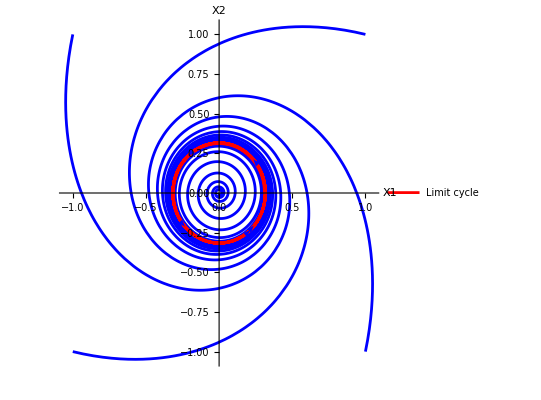

```mathematica
ClearAll["Global`*"]

X1dot[X1_,X2_] := (1/10)* X1-X2^3-X1 *X2^2-X1^2 *X2-X2-X1^3
X2dot[X1_,X2_] := X1+(1/10)* X2+X1 *X2^2+X1^3-X2^3-X1^2 *X2

initialConditions=Flatten[Table[{x,y},{x,-1,1,0.2},{y,-1,1,0.2}],1];

initialConditions = Join[
{{-0.01,-0.01}},{{1,1}},{{-1,1}},{{1,-1}},{{-1,-1}}
];


solutions=Table[NDSolve[{
X1'[t]==X1dot[X1[t],X2[t]],
X2'[t]==X2dot[X1[t],X2[t]],
X1[0]==init[[1]],
X2[0]==init[[2]]},
{X1,X2},{t,0,50}],
{init,initialConditions}];

limitCycleSolution=NDSolve[{
X1'[t]==X1dot[X1[t],X2[t]],
X2'[t]==X2dot[X1[t],X2[t]],
X1[0]==0.31,
X2[0]==0 },
{X1,X2},{t,0,1000} ];

arrows = Table[{0.03,t},{t,0,1,0.05}];

p1=ParametricPlot[Evaluate[Table[{X1[t],X2[t]}/. sol,{sol,solutions}]],{t,0,50},
PlotRange->All,
AxesLabel->{"X1","X2"},
PlotStyle->Blue]/. Line[x_]:>{Arrowheads[arrows],Arrow[x]};

p2=ParametricPlot[Evaluate[{X1[t],X2[t]}/. limitCycleSolution],{t,0,50},
PlotStyle->Red,PlotLegends->{"Limit cycle"}
];

Show[p1,p2]
```

### task c)

```mathematica
ClearAll["Global`*"]
X1[r_,θ_]= r*Cos[θ];
X2[r_,θ_]= r*Sin[θ];

X1computed[r_,θ_] = D[X1[r[t],θ[t]],t] // FullSimplify
X2computed[r_,θ_] = D[X2[r[t],θ[t]],t] // FullSimplify
```

Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]

Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]

```mathematica
X1dot[X1_,X2_] = (1/10)* X1[r,θ]-X2[r,θ]^3-X1[r,θ] *X2[r,θ]^2-X1[r,θ]^2 *X2[r,θ]-X2[r,θ]-X1[r,θ]^3  // FullSimplify
X2dot[X1_,X2_] = X1[r,θ]+(1/10)* X2[r,θ]+X1[r,θ] *X2[r,θ]^2+X1[r,θ]^3-X2[r,θ]^3-X1[r,θ]^2 *X2[r,θ]  // FullSimplify
```

(r/10-r^3) Cos[θ]-r (1+r^2) Sin[θ]

(r+r^3) Cos[θ]+(r/10-r^3) Sin[θ]

```mathematica
rdot[r_,μ_] = μ*r-r^3
θdot[ω_,r_,ν_] = ω+ν*r^2
```

-r^3+r μ

r^2 ν+ω

By comparing constants of the computed xdot and the given xdot (eq 2) we find that μ = 1/10, ν = 1, ω = 1.

### task d)

Part::partd: Part specification InterpolatingFunction[{{0.,5.71199}},{5,3,1,{69},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.000140231,«48»,«19»}},{{{{1.,0.},{0.,1.}},{{-0.2,-1.1},{1.3,0.}}},{{{0.999972,-0.000154254},{0.000182291,1.}},{{-0.200226,-1.1},{1.29993,-0.000169677}}},«48»,«19»},{Automatic}][t]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification InterpolatingFunction[{{0.,5.71199}},{5,3,1,{69},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.000140231,«48»,«19»}},{{{{1.,0.},{0.,1.}},{{-0.2,-1.1},{1.3,0.}}},{{{0.999972,-0.000154254},{0.000182291,1.}},{{-0.200226,-1.1},{1.29993,-0.000169677}}},«48»,«19»},{Automatic}][t]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of InterpolatingFunction[{{0.,5.71199}},{5,3,1,{69},{4},0,0,0,0,Automatic,{},{},False},{{0.,0.000140231,«48»,«19»}},{{{{1.,0.},{0.,1.}},{{-0.2,-1.1},{1.3,0.}}},{{{0.999972,-0.000154254},{0.000182291,1.}},{{-0.200226,-1.1},{1.29993,-0.000169677}}},«48»,«19»},{Automatic}][t] does not exist.

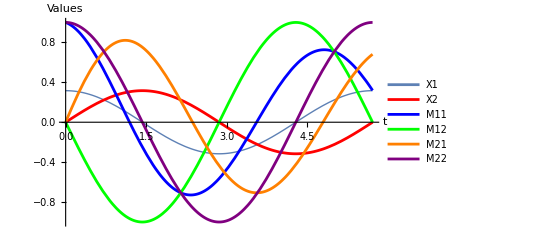

```mathematica
ClearAll["Global`*"]
r0=Sqrt[1/10];
T=2 π/((1/10)+1);
M0=IdentityMatrix[2];

X1dot[X1_,X2_]:=(1/10)*X1-X2^3-X1*X2^2-X1^2*X2-X2-X1^3;
X2dot[X1_,X2_]:=X1+(1/10)*X2+X1*X2^2+X1^3-X2^3-X1^2*X2;

jacobi=D[{X1dot[X1,X2],X2dot[X1,X2]},{{X1,X2}}];

MPrime[M_,X_]:=(jacobi/. {X1->X[[1]],X2->X[[2]]}).M;

solution=NDSolve[{
X1'[t] == X1dot[X1[t],X2[t]],
X2'[t] == X2dot[X1[t],X2[t]],
M'[t]==MPrime[M[t],{X1[t],X2[t]}],
X1[0]==r0,
X2[0]==0,
M[0]==M0},
{X1,X2,M},{t,0,T}];

solM[t_]=M[t] /.solution[[1]];

solX[t_] = {X1[t],X2[t]} /. solution[[1]];

X1[t_]:=solX[t][[1]];
X2[t_]:=solX[t][[2]];
M11[t_]:=solM[t][[1,1]];
M12[t_]:=solM[t][[1,2]];
M21[t_]:=solM[t][[2,1]];
M22[t_]:=solM[t][[2,2]];


Plot[Evaluate[{X1[t],X2[t],M11[t],M12[t],M21[t],M22[t]}],{t,0,T},PlotLegends->{"X1","X2","M11","M12","M21","M22"},
PlotRange->Full,
PlotStyle->{Thick,Red,Blue,Green,Orange,Purple,Magenta},
AxesLabel->{"t","Values"}]
```

### task e)

```mathematica
solM[T]
```

{{0.319053,2.12317×10^-8},{0.680947,1.}}

### task f)

```mathematica
eig = Eigenvalues[solM[T]];
σ = (1/T)*Log[eig]
```

Set::write: Tag Times in  σ is Protected.

{5.78753×10^-9,-0.2}

### task g)

```mathematica
ClearAll["Global`*"]
T=2 π/((1/10)+1);

JgI[r_,θ_]={{Cos[θ],-r Sin[θ]},{Sin[θ],r Cos[θ]}};
Jg[r_,θ_]=Inverse[JgI[r,θ]];

rdot[r_]:=(1/10)*r-r^3;
θdot[r_]:=1+r^2;

r0=Sqrt[1/10];
θ0=0;

Mcart0=IdentityMatrix[2];
Mpol0=JgI[r0,θ0].Mcart0.Jg[r0,θ0]; 

Jpolar=D[{rdot[r],θdot[r]},{{r,θ}}]; 

Mpol=Mpol0.MatrixExp[Jpolar*T]; 

Mcart[r_,θ_]=JgI[r,θ].Mpol.Jg[r,θ];

.08sol = Mcart[r0,θ0]
```

{{ⅇ^(-4 π/11),0},{1-ⅇ^(-4 π/11),1}}

### task h)

```mathematica
eig = Eigenvalues[Mcart[r0,θ0]];
σ = (1/T)*Log[eig]
```

{0,-1/5}